```mathematica
NS[]
```

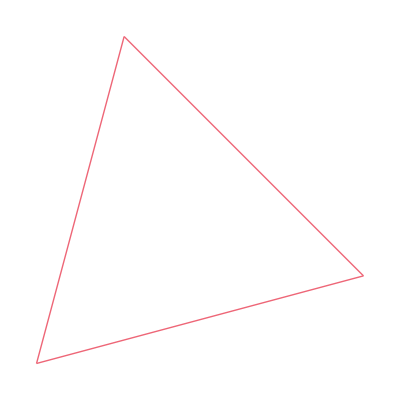

```mathematica
ClearAll[repr];n=2;
Co[x_]:=Flatten@{1-Total@Flatten@x,x};
u=Table[1,n+1];repr[f_]:=IdentityMatrix[{n,n+1}].RotationMatrix[{u,{0,0,1}}].f;
simp=Graphics[Sequence@@{red,Line[#]}&/@T/@(repr/@T/@Subsets[IdentityMatrix[n+1],{2}])]
```

```mathematica
freq[data_]:=(#/Total@#)&@(Count[data,#]&/@Range[3]);
```

```mathematica
ClearAll[f];MF/@(Evaluate[Array[f,3]]=Permutations[{6,1,1}/8])
```

{(3/4
1/8
1/8),(1/8
3/4
1/8),(1/8
1/8
3/4)}

```mathematica
post[data_]:=Block[{tab=Table[Times@@((f[m][[#]])&/@data),{m,3}]},tab/Total[tab]]
```

```mathematica
pred[data_]:=post[data].T[Array[f,3]]
```

```mathematica
lsc[data_]:=Table[Mean[Table[Log[f[m][[data[[i]]]]],{i,1,t}]],{m,3}];
```

```mathematica
SeedRandom[666];ft=(#/Total@#)&@(4*f[1]+5*f[2]+6*f[3]);data=RandomChoice[ft->Range[3],500];
```

```mathematica
{ft,(fe=freq[data])}//N
```

{{0.291667,0.333333,0.375},{0.27,0.366,0.364}}

```mathematica
MF/@(seqpost=Table[post[data[[;;t]]],{t,Length@data}])//N;
```

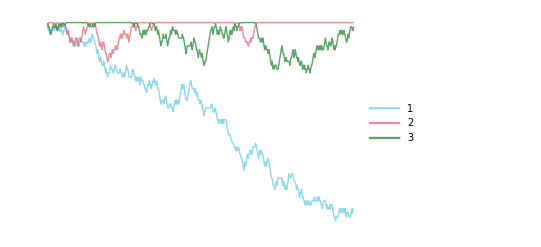

```mathematica
ListLogPlot[T@seqpost,Joined->True,PlotRange->{All,All},PlotRangeClipping->False,PlotStyle->Directive[{Opacity[0.75],solid}],PlotLegends->Placed[Range[3],{Left,Bottom}]]
```

```mathematica
seqpostp=ListPlot[repr/@seqpost,Joined->True,PlotRange->All,PlotMarkers->Auto];
Show[{simp,seqpostp,Graphics[{green,PointSize[Large],Point[repr@ft],yellow,PointSize[Large],Point[repr@fe]}]}]
```

```mathematica
Animate[Show[{simp,Graphics[{Black,Text[t,repr@seqpost[[t]]],yellow,Opacity[0.5],PointSize[Large],Point[repr@seqpost[[t]]],green,PointSize[Large],Point[repr@ft],yellow,PointSize[Large],Point[repr@fe]}]}],{t,1,Length@data,1},AnimationRate->2]
```

```mathematica
MF/@(seqlsc=Table[lsc[data[[;;t]]],{t,Length@data}])//N;
```

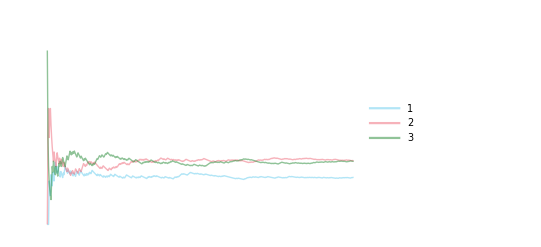

```mathematica
ListPlot[T@seqlsc,Joined->True,PlotRange->{All,All},PlotRangeClipping->False,PlotStyle->Directive[{Opacity[0.5],solid}],PlotLegends->Placed[Range[3],{Center,Top}]]
```

```mathematica
(MF/@(seqpred=Table[pred[data[[;;t]]],{t,Length@data}]))//N
```

{(0.203125
0.203125
0.59375),(0.173077
0.413462
0.413462),(0.139535
0.648256
0.212209),(0.203125
0.59375
0.203125),(0.141447
0.717105
0.141447),(0.127867
0.744266
0.127867),(0.141816
0.730381
0.127803),(0.141447
0.717105
0.141447),(0.139535
0.648256
0.212209),(0.203125
0.59375
0.203125),(0.173077
0.413462
0.413462),(0.139535
0.648256
0.212209),(0.203125
0.59375
0.203125),(0.413462
0.413462
0.173077),(0.333333
0.333333
0.333333),(0.203125
0.59375
0.203125),(0.141447
0.717105
0.141447),(0.212209
0.648256
0.139535),(0.203125
0.59375
0.203125),(0.173077
0.413462
0.413462),(0.139535
0.648256
0.212209),(0.133562
0.433219
0.433219),(0.173077
0.413462
0.413462),(0.139535
0.648256
0.212209),(0.133562
0.433219
0.433219),(0.12747
0.213933
0.658597),(0.139535
0.212209
0.648256),(0.133562
0.433219
0.433219),(0.173077
0.413462
0.413462),(0.333333
0.333333
0.333333),(0.203125
0.203125
0.59375),(0.141447
0.141447
0.717105),(0.127867
0.127867
0.744266),(0.127803
0.141816
0.730381),(0.141447
0.141447
0.717105),(0.127867
0.127867
0.744266),(0.125482
0.125482
0.749037),(0.12508
0.12508
0.749839),(0.125482
0.12508
0.749438),(0.125482
0.125482
0.749037),(0.12508
0.12508
0.749839),(0.12508
0.125482
0.749438),(0.125013
0.12508
0.749906),(0.12508
0.12508
0.749839),(0.125013
0.125013
0.749973),(0.125013
0.12508
0.749906),(0.125013
0.125482
0.749505),(0.12508
0.125482
0.749438),(0.125482
0.125482
0.749037),(0.12508
0.12508
0.749839),(0.125013
0.125013
0.749973),(0.125013
0.12508
0.749906),(0.125013
0.125482
0.749505),(0.12508
0.125482
0.749438),(0.125482
0.125482
0.749037),(0.12508
0.12508
0.749839),(0.12508
0.125482
0.749438),(0.12508
0.12788
0.74704),(0.125078
0.14189
0.733032),(0.125069
0.214276
0.660655),(0.125013
0.141892
0.733095),(0.125078
0.14189
0.733032),(0.125013
0.12788
0.747107),(0.125013
0.141892
0.733095),(0.125078
0.14189
0.733032),(0.125069
0.214276
0.660655),(0.12504
0.43748
0.43748),(0.125241
0.437379
0.437379),(0.125069
0.660655
0.214276),(0.125413
0.66036
0.214227),(0.125241
0.437379
0.437379),(0.125069
0.660655
0.214276),(0.125413
0.66036
0.214227),(0.12747
0.658597
0.213933),(0.126443
0.436778
0.436778),(0.125413
0.66036
0.214227),(0.125241
0.437379
0.437379),(0.125069
0.660655
0.214276),(0.12504
0.43748
0.43748),(0.125011
0.214284
0.660704),(0.125002
0.141892
0.733106),(0.125
0.12788
0.747119),(0.125002
0.12788
0.747118),(0.125
0.125482
0.749518),(0.125
0.12508
0.74992),(0.125
0.125013
0.749987),(0.125
0.125013
0.749987),(0.125
0.12508
0.74992),(0.125
0.125013
0.749987),(0.125
0.125002
0.749998),(0.125
0.125013
0.749987),(0.125
0.12508
0.74992),(0.125
0.12508
0.74992),(0.125
0.125013
0.749987),(0.125
0.125002
0.749998),(0.125
0.125
0.75),(0.125
0.125
0.75),(0.125
0.125
0.75),(0.125
0.125
0.75),(0.125
0.125
0.75)}

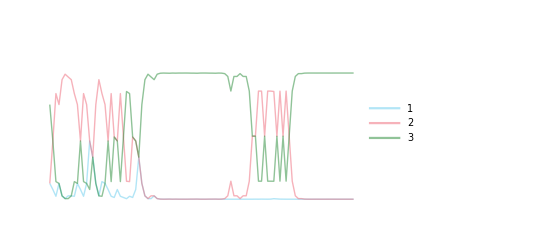

```mathematica
ListPlot[T@seqpred,Joined->True,PlotRange->{All,{0,1}},PlotRangeClipping->False,PlotStyle->Directive[{Opacity[0.5],solid}],PlotLegends->Placed[Range[3],{Center,Right}]]
```

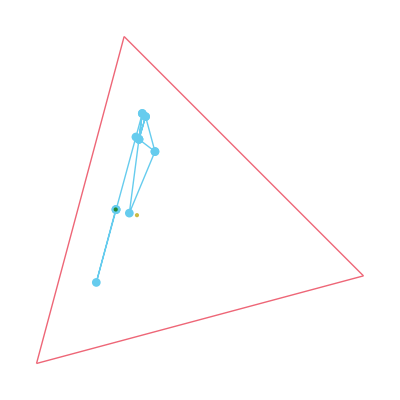

```mathematica
seqpredp=ListPlot[repr/@seqpred,Joined->True,PlotRange->All,PlotMarkers->Auto];
Show[{simp,seqpredp,Graphics[{green,PointSize[Large],Point[repr@ft],yellow,PointSize[Large],Point[repr@fe]}]}]
```

```mathematica
Animate[Show[{simp,Graphics[{Black,Text[t,repr@seqpred[[t]]],yellow,Opacity[0.5],PointSize[Large],Point[repr@seqpred[[t]]],green,PointSize[Large],Point[repr@ft],yellow,PointSize[Large],Point[repr@fe]}]}],{t,1,Length@data,1},AnimationRate->Auto]
```